```mathematica
totalo[x_Integer?Positive] := Apply[Plus, Select[Range[1,x], OddQ]]
```

```mathematica
totalo[99]
```

2500

```mathematica
middle[x_Integer?OddQ] := (x+1)/2
```

```mathematica
middle[10]
```

middle[10]

```mathematica
middle[11]
```

6

```mathematica
triangle[x_] := If[Abs[x] < 1, 1-Abs[x], 0]
```

```mathematica
triangle[2]
```

0

```mathematica
triangle[0.01]
```

0.99

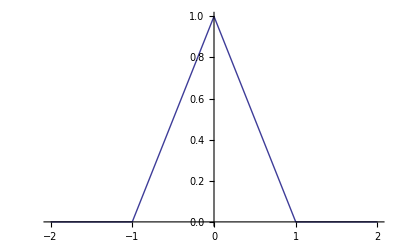

```mathematica
Plot[triangle[x], {x,-2,2}]
```

```mathematica
lslist[x_List] := {Length[x], Plus@@x}
```

```mathematica
lslist[{1,2,3,4}]
```

{4,10}

```mathematica
iplist[x_List, y_List]  := Plus@@MapThread[Times,{x,y}]
```

```mathematica
iplist[{1,2,3}, {4,5,6}]
```

32

```mathematica
tau[x_Integer?Positive] := Length[Divisors[x]]
```

```mathematica
tau[2]
```

2

```mathematica
tau[10]
```

4

```mathematica
rsigma[n_Integer?Positive]:=Plus @@ Map[1/#&, Divisors[n]]
```

```mathematica
rsigma[6]
```

2

```mathematica
rsigma[28]
```

2

```mathematica
rsigma[496]
```

2

```mathematica
rsigma[8128]
```

2

6, 28, 496, and 8128 are perfect numbers.  The answer is always two for any perfect number n because all the fractions can be written so that the denominator is n.  Then the numerators become the divisors of n, so the sum is (2n)/n which is 2.

```mathematica
nu[n_Integer?Positive] := Length[FactorInteger[n]]
```

```mathematica
nu[10]
```

2

```mathematica
mu[n_Integer?Positive] := If[n ==1, 1,If [Fold[#1 || (#2[[2]] ≥2)&,False, FactorInteger[n]], 0,(-1)^nu[n]]]
```

```mathematica
sumdmu[n_Integer?Positive]:= Plus @@ Map[mu, Divisors[n]]
```

To find the GCD using the prime factorization, create a new number repesented by its prime factorization.  For each prime, have the exponent be the lowest of the two exponents found in the numbers you're finding the GCD of.  Do not include factors that occur only in one product.

```mathematica
FactorIntegerGCD[m_Integer,n_Integer] := Module[{x = FactorInteger[m], y = FactorInteger[n], a = 1}, While[x ≠ {} && y≠ {}, If[x[[1]][[1]] ==y[[1]][[1]], a = a * x[[1]][[1]]^Min[x[[1]][[2]], y[[1]][[2]]]; x = Rest[x]; y=Rest[y], If[x[[1]][[1]] > y[[1]][[1]], y = Rest[y], x = Rest[x]]]]; a]
```

```mathematica
FactorIntegerGCD[60,40]
```

20

```mathematica
FactorIntegerGCD[66,66]
```

11

```mathematica
FactorIntegerGCD::"usage"="FactorIntegerGCD[m,n] returns the largest positive integer that divides of m and n without a remainder."
```

FactorIntegerGCD[m,n] returns the largest positive integer that divides of m and n without a remainder.

```mathematica
?FactorIntegerGCD
```

FactorIntegerGCD[m,n] returns the largest positive integer that divides of m and n without a remainder.

```mathematica
sumdmu::"usage"="sumdmu[n] returns the sum of the numbers mu(d) for each divisor d of n."
```

sumdmu[n] returns the sum of the numbers mu(d) for each divisor d of n.

```mathematica
mu::"usage"= "mu[n] returns 0 if n has a factor that is a perfect square, 1 if n is 1, and (-1)^nu(n) otherwise."
```

mu[n] returns 0 if n has a factor that is a perfect square, 1 if n is 1, and (-1)^nu(n) otherwise.

```mathematica
nu::"usage" = "nu[n] returns the number of distinct prime factors of n"
```

nu[n] returns the number of distinct prime factors of n

```mathematica
rsigma::"usage" = "rsigma[n] returns the sum of the recipricals of the divisors of a positive integer n"
```

rsigma[n] returns the sum of the recipricals of the divisors of a positive integer n

```mathematica
tau::"usage" = "tau[n] returns the number of divisors of n"
```

tau[n] returns the number of divisors of n

```mathematica
iplist::"usage" = "iplist[x,y] returns the dot product of two lists x and y (i.e the sum of the elementwise product of x and y)"
```

iplist[x,y] returns the dot product of x and y (i.e the sum of the elementwise product of x and y)

```mathematica
lslist::"usage" = "lslist[n] returns a list consisting of the length and sum of the elements of n"
```

lslist[n] returns a list consisting of the length and sum of the elements of n

```mathematica
triangle::"usage" = "triangle[x] returns 1 - Abs[x] if Abs[x] is less then 1 and 0 otherwise"
```

triangle[x] returns 1 - Abs[x] if Abs[x] is less then 1 and 0 otherwise

```mathematica
middle::"usage" = "middle[x] returns (x+1)/2 given an odd integer x"
```

middle[x] returns (x+1)/2 given an odd integer x

```mathematica
totalo::"usage" = "totalo[x] returns the sum of the positive odd integers less than or equal to x"
```

totalo[x] returns the sum of the positive odd integers less than or equal to x